```mathematica
Exit[]
```

```mathematica
a=7297352537.6*10^-12;M=510998.910;Z=1;k=-1;
Energie[n_]:=M*(1-1/Sqrt[1+(Z*a/(n-Abs[k]+Sqrt[k^2-(Z*a)^2]))^2]);Table[N[Energie[i]],{i,10}]
```

{13.6059,3.40148,1.51176,0.850365,0.544233,0.377939,0.277669,0.21259,0.167972,0.136058}

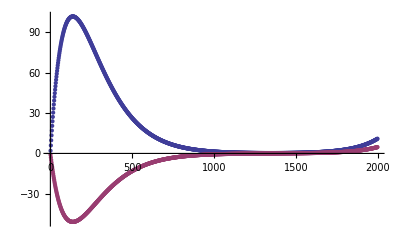

```mathematica
f[u_,r_]:=Simplify[{(Z*a/r+2-Enn)*u[[2]]-k/r*u[[1]],
k/r*u[[2]]+(Enn-Z*a/r)*u[[1]]}];
k=-1;Z=1;U=.
n=1000;
h=2000/n;
Enn=13.6059/M;
u={(91.35044102604739 (-3.662751763692355+Enn) (1.6262886176197724+Enn))/((-0.0109728221664999+Enn) (181.38339842774778+Enn)),-1};
r=1;U={{r,u}};
Do[
k0=h*f[u,r];k1=h*f[u+k0/2,r+h/2];k2=h*f[u+k1/2,r+h/2];k3=h*f[u+k2,r+h];
u+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[U,{r,u}],{n}];x=.;
ListPlot[Table[{#[[1]],137^(i-2)*#[[2,i]]}&/@U[[1;;n]],{i,2}]//N,PlotRange->All]
```

```mathematica
X[1000]
```

π/4

```mathematica
X[1000]/n
```

1/10

```mathematica
-g[
```

```mathematica
lambda[n_]:=Sqrt[1-(1-En[n]/M)^2];
gamma:=Sqrt[k^2-Z^2*a^2];f[r_,n_,k_]:=-r^gamma*Exp[-lambda[n]*r]*(((n-1+gamma)/(1-En[n]/M)-k)*Hypergeometric1F1[-(n-1),2*gamma+1,2*lambda[n]*r]+(n-1)*Hypergeometric1F1[1-(n-1),2*gamma+1,2*lambda[n]*r]);g[r_,n_,k_]:=Sqrt[2*M/En[n]-1]*r^gamma*Exp[-lambda[n]*r]*(((n-1+gamma)/(1-En[n]/M)-k)*Hypergeometric1F1[-(n-1),2*gamma+1,2*lambda[n]*r]-(n-1)*Hypergeometric1F1[1-(n-1),2*gamma+1,2*lambda[n]*r]);
```

```mathematica
g[1,1,-1]/f[1,1,-1]
```

-274.068

# Randbedingungen

## r << 1

```mathematica
Exit[]
```

```mathematica
a=7297352537.6*10^-12;M=510998.910;k=-1;Z=1;
```

```mathematica
Energie[n_]:=M*(1-1/Sqrt[1+(Z*a/(n-Abs[k]+Sqrt[k^2-(Z*a)^2]))^2]);Table[N[Energie[i]],{i,10}]
```

{13.6059,3.40148,1.51176,0.850365,0.544233,0.377939,0.277669,0.21259,0.167972,0.136058}

```mathematica
f[u_,r_]:=Simplify[{(Z*a/r+2-En)*u[[2]]-k/r*u[[1]],
k/r*u[[2]]+(En-Z*a/r)*u[[1]]}];
```

```mathematica
u:=r^(s+n)*{a[n],b[n]}
```

```mathematica
Collect[Simplify[(f[u,r]-D[u,r])/r^(s-1)],r]//MatrixForm
```

(-(-2+En) r^(1+n) b[n]-r^n ((k+n+s) a[n]-a Z b[n])
En r^(1+n) a[n]+r^n (-a Z a[n]+(k-n-s) b[n]))

## =>

```mathematica
13.605873075061169
```

```mathematica
s=Sqrt[k^2-(Z*a)^2];
```

```mathematica
En=.;Simplify[Inverse[{{Z*a/En,(n+s-k)/En},{(n+s+k)/(2-En),Z*a/(En-2)}}]]
S[n_,En_]:={{(a En Z)/(n^2+2 n √(k^2-a^2 Z^2)),-((-2+En) (-k+n+√(k^2-a^2 Z^2)))/(n (n+2 √(k^2-a^2 Z^2)))},{(En (k+n+√(k^2-a^2 Z^2)))/(n (n+2 √(k^2-a^2 Z^2))),(a (-2+En) Z)/(n (n+2 √(k^2-a^2 Z^2)))}};
DS[n_,En_]:={{(a Z)/(n^2+2 n √(k^2-a^2 Z^2)),-(-k+n+√(k^2-a^2 Z^2))/(n (n+2 √(k^2-a^2 Z^2)))},{(k+n+√(k^2-a^2 Z^2))/(n (n+2 √(k^2-a^2 Z^2))),(a Z)/(n (n+2 √(k^2-a^2 Z^2)))}};
S[m,En]//MatrixForm
DS[m,En]//MatrixForm
```

{{(a En Z)/(-k^2+n^2+2 n s+s^2+a^2 Z^2),((-2+En) (k-n-s))/(-k^2+n^2+2 n s+s^2+a^2 Z^2)},{(En (k+n+s))/(-k^2+n^2+2 n s+s^2+a^2 Z^2),(a (-2+En) Z)/(-k^2+n^2+2 n s+s^2+a^2 Z^2)}}

((a En Z)/(m^2+2 m √(k^2-a^2 Z^2)) | -((-2+En) (-k+m+√(k^2-a^2 Z^2)))/(m (m+2 √(k^2-a^2 Z^2)))
(En (k+m+√(k^2-a^2 Z^2)))/(m (m+2 √(k^2-a^2 Z^2))) | (a (-2+En) Z)/(m (m+2 √(k^2-a^2 Z^2))))

((a Z)/(m^2+2 m √(k^2-a^2 Z^2)) | -(-k+m+√(k^2-a^2 Z^2))/(m (m+2 √(k^2-a^2 Z^2)))
(k+m+√(k^2-a^2 Z^2))/(m (m+2 √(k^2-a^2 Z^2))) | (a Z)/(m (m+2 √(k^2-a^2 Z^2))))

```mathematica
UN[R_,N_,En_]:=Module[{u={1,(k+s)/Z/a},U={1,(k+s)/Z/a}*R^s},
For[n=1,n<N,n++,
u=S[n,En].u;
U+=u*R^(s+n);
];

U]
```

```mathematica
U[r_,g_,En_]:=Module[{u={1,(k+s)/Z/a},U={0,0},DU={0,0},du={0,0},n=0},
Label[begin];
U+=u*r^(s+n);
DU+=du*r^(s+n);
n++;
du=DS[n,En].u+S[n,En].du;
u=S[n,En].u;
If[(#[[1]]>g  || #[[2]]>g)&[Abs[u*R^(s+n)/U/.r->R]],Goto[begin]];
{n,U,DU}]
```

```mathematica
R=1000;g=0.01;rU=U[r,g,1/M];Plot[{rU[[2,1]],rU[[2,2]]*137},{r,0,R},PlotRange->All]
```

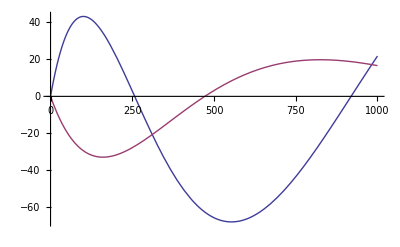

```mathematica
EN[iEn_,g2_]:=Module[{rU,fU,n=0,i,En=iEn,ll},
Label[begin];
fU=U[r,g,En];

rU=fU/.r->R;

If[rU[[2,1]]*rU[[2,2]]>0,

En-=(rU[[2,1]]+rU[[2,2]])/(rU[[3,1]]+rU[[3,2]]);

n++
Goto[begin];
];

{n,En*M,Abs[rU[[2,1]]-rU[[2,2]]]}
]
```

```mathematica
R=3000;g=0.001;EN[13/M,0.1]
```

{8,13.6059,0.000441718}

```mathematica
-  {0,13.605873075061169
```

```mathematica
R=2000;g=0.001;
```

```mathematica
plot[{rU[[2,1]],rU[[3,1]]},100,R]
```

```mathematica
En=4/M;rU[[2,1]]
```

129.072

```mathematica
n=0;x
```

10

```mathematica
n=0;While[x=n;x<10,n++;Print[n]]
```

1

2

3

4

5

6

7

8

9

10

{r^2/4,-Csc[11] Sin[10 r]}

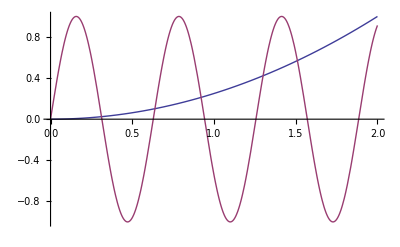

```mathematica
plot[liste_,R_]:=Module[{nN=100,table,max,st={Red,Green,Blue}},
liste/(Max[Abs[#]]&/@(Table[#/.r->i*R/nN,{i,0,nN}]&/@liste))
]
ll=plot[{r^2,Sin[10*r]},2]
Plot[ll,{r,0,2}]
```

## r gegen Inifinity

```mathematica
Exit[]
```

```mathematica
M=510998.910;a=7297352537.6*10^-12;
```

```mathematica
a=7297352537.6*10^-12;M=510998.910;k=-1;Z=1;
```

```mathematica
Energie[n_]:=M*(1-1/Sqrt[1+(Z*a/(n-Abs[k]+Sqrt[k^2-(Z*a)^2]))^2]);Table[N[Energie[i]],{i,10}]
```

```mathematica
$Assumptions=1>En>0;
```

```mathematica
s=(En-1)*Z*a/L;L:=Sqrt[(2-En)*En];L=.;s=.
```

```mathematica
f[u_,r_]:=Simplify[{(Z*a/r+2-En)*u[[2]]-k/r*u[[1]],
k/r*u[[2]]+(En-Z*a/r)*u[[1]]}];
```

```mathematica
u=.
```

```mathematica
U={(hb[r]-ha[r])*L/En,hb[r]+ha[r]}*Exp[-r*L];
```

```mathematica
#[[2]]&/@Simplify[Solve[Simplify[(f[U,r]-D[U,r])/Exp[-r*L]*En*r]==0,{ha'[r],hb'[r]}][[1]]]/.ha[r]->u[[1]]/.hb[r]->u[[2]]/.r->rr
```

Part::partd: Part specification u ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification u ⟦ 2 ⟧ is longer than depth of object.

{1/(2 En L rr)((En^3 rr+En L^2 rr+a L^2 Z-En^2 (2 rr+a Z)) u⟦1⟧+(En^3 rr+En L (2 k+L rr)-a L^2 Z-En^2 (2 rr+a Z)) u⟦2⟧),1/(2 En L rr)((-En^3 rr+En L (2 k-L rr)+a L^2 Z+En^2 (2 rr+a Z)) u⟦1⟧+(-En^3 rr+3 En L^2 rr-a L^2 Z+En^2 (2 rr+a Z)) u⟦2⟧)}

```mathematica
F[u_,rr_]:=Simplify[{(-a (-1+En) Z u⟦1⟧+(√(-(-2+En) En) k-a Z) u⟦2⟧)/(√(-(-2+En) En) rr),((√(-(-2+En) En) k+a Z) u⟦1⟧+(4 En rr-2 En^2 rr-a Z+a En Z) u⟦2⟧)/(√(-(-2+En) En) rr)}]
```

```mathematica
r[x_]:=1/x;u:={a[n],b[n]}*x^(n+s)
```

```mathematica
g1=Collect[Simplify[(F[u,r[x]]*D[r[x],x]-D[u,x])*x^(2-s)],{a[n],b[n]}];g1
```

{-(x^(1+n) (a (-1+En) √(-(-2+En) En) Z+L (√(-(-2+En) En) n+a Z-a En Z)) a[n])/(√(-(-2+En) En) L)-(x^(1+n) (√(-(-2+En) En) k-a Z) b[n])/(√(-(-2+En) En)),-(x^(1+n) (√(-(-2+En) En) k+a Z) a[n])/(√(-(-2+En) En))-1/(√(-(-2+En) En) L)x^n (-2 En^2 L+x (√(-(-2+En) En) L n-a √(-(-2+En) En) Z-a L Z)+En (4 L+a √(-(-2+En) En) x Z+a L x Z)) b[n]}

```mathematica
g2:={x^n (-n) a[n]+x^n (-k+a Z/L) b[n],-x^(1+n) ( k+a Z/L) a[n]+x^n (-n x-2 s x+-2*L) b[n]};g2//MatrixForm
```

(-n x^n a[n]+x^n (-k+(a Z)/L) b[n]
-x^(1+n) (k+(a Z)/L) a[n]+x^n (-2 L-n x-2 s x) b[n])

```mathematica
a[n_]:=(Z*a/L-k)/n*b[n]
```

```mathematica
g2[[2]]
```

x^n (-2 L-n x-2 s x) b[n]-(x^(1+n) (-k+(a Z)/L) (k+(a Z)/L) b[n])/n

```mathematica
M1={{L,2-En},{En,L}};Eigenvalues[M1];B=Transpose[Eigenvectors[M1]];
```

```mathematica
$Assumptions=1>En>0
```

1>En>0

## =>

```mathematica
a[n_]:=(Z*a/L-k)/n*b[n]
```

```mathematica
b[n_]:=b0*Product[((k^2-a^2*Z^2/L^2)/i-(i+2*s))/2/L,{i,1,n}]
```

```mathematica
b[4]
```

(b0 (-1+k^2-2 s-(a^2 Z^2)/L^2) (-4-2 s+1/4 (k^2-(a^2 Z^2)/L^2)) (-3-2 s+1/3 (k^2-(a^2 Z^2)/L^2)) (-2-2 s+1/2 (k^2-(a^2 Z^2)/L^2)))/(16 L^4)

```mathematica
((k^2-a^2*Z^2/L^2)/i-(i+2*s))/2/L
```

```mathematica
Exit[];
```

```mathematica
#[[1,2]]&/@Solve[(-i-(2 a (-1+En) Z)/(√((2-En) En))+(k^2-(a^2 Z^2)/((2-En) En))/i)/(2 √((2-En) En))==0,En]
```

{Root[-4.803202207768027100482068692831×10^47 Z^4+Z^2 (3.607947473061402710515109288209×10^52 i^2+3.607947473061402754471055780591×10^52 k^2+2.401601103884013550241034346415×10^47 Z^2) #1+(-6.775315927423285688056806651456×10^56 i^4+1.355063185484657137611361330291×10^57 i^2 k^2-6.775315927423285688056806651456×10^56 k^4-1.803973736530701492568802543056×10^53 i^2 Z^2-3.607947473061402754471055780591×10^52 k^2 Z^2) #1^2+(1.016297389113492853208520997718×10^57 i^4-2.032594778226985706417041995437×10^57 i^2 k^2+1.016297389113492853208520997718×10^57 k^4+2.254967170663376900038815153558×10^53 i^2 Z^2+9.019868682653506886177639451477×10^51 k^2 Z^2) #1^3+(-5.081486945567464266042604988592×10^56 i^4+1.016297389113492853208520997718×10^57 i^2 k^2-5.081486945567464266042604988592×10^56 k^4-1.082384241918420884007954060557×10^53 i^2 Z^2) #1^4+(8.46914490927910711007100831432×10^55 i^4-1.693828981855821422014201662864×10^56 i^2 k^2+8.46914490927910711007100831432×10^55 k^4+1.8039737365307013662465412672×10^52 i^2 Z^2) #1^5&,1],Root[-4.803202207768027100482068692831×10^47 Z^4+Z^2 (3.607947473061402710515109288209×10^52 i^2+3.607947473061402754471055780591×10^52 k^2+2.401601103884013550241034346415×10^47 Z^2) #1+(-6.775315927423285688056806651456×10^56 i^4+1.355063185484657137611361330291×10^57 i^2 k^2-6.775315927423285688056806651456×10^56 k^4-1.803973736530701492568802543056×10^53 i^2 Z^2-3.607947473061402754471055780591×10^52 k^2 Z^2) #1^2+(1.016297389113492853208520997718×10^57 i^4-2.032594778226985706417041995437×10^57 i^2 k^2+1.016297389113492853208520997718×10^57 k^4+2.254967170663376900038815153558×10^53 i^2 Z^2+9.019868682653506886177639451477×10^51 k^2 Z^2) #1^3+(-5.081486945567464266042604988592×10^56 i^4+1.016297389113492853208520997718×10^57 i^2 k^2-5.081486945567464266042604988592×10^56 k^4-1.082384241918420884007954060557×10^53 i^2 Z^2) #1^4+(8.46914490927910711007100831432×10^55 i^4-1.693828981855821422014201662864×10^56 i^2 k^2+8.46914490927910711007100831432×10^55 k^4+1.8039737365307013662465412672×10^52 i^2 Z^2) #1^5&,2],Root[-4.803202207768027100482068692831×10^47 Z^4+Z^2 (3.607947473061402710515109288209×10^52 i^2+3.607947473061402754471055780591×10^52 k^2+2.401601103884013550241034346415×10^47 Z^2) #1+(-6.775315927423285688056806651456×10^56 i^4+1.355063185484657137611361330291×10^57 i^2 k^2-6.775315927423285688056806651456×10^56 k^4-1.803973736530701492568802543056×10^53 i^2 Z^2-3.607947473061402754471055780591×10^52 k^2 Z^2) #1^2+(1.016297389113492853208520997718×10^57 i^4-2.032594778226985706417041995437×10^57 i^2 k^2+1.016297389113492853208520997718×10^57 k^4+2.254967170663376900038815153558×10^53 i^2 Z^2+9.019868682653506886177639451477×10^51 k^2 Z^2) #1^3+(-5.081486945567464266042604988592×10^56 i^4+1.016297389113492853208520997718×10^57 i^2 k^2-5.081486945567464266042604988592×10^56 k^4-1.082384241918420884007954060557×10^53 i^2 Z^2) #1^4+(8.46914490927910711007100831432×10^55 i^4-1.693828981855821422014201662864×10^56 i^2 k^2+8.46914490927910711007100831432×10^55 k^4+1.8039737365307013662465412672×10^52 i^2 Z^2) #1^5&,3],Root[-4.803202207768027100482068692831×10^47 Z^4+Z^2 (3.607947473061402710515109288209×10^52 i^2+3.607947473061402754471055780591×10^52 k^2+2.401601103884013550241034346415×10^47 Z^2) #1+(-6.775315927423285688056806651456×10^56 i^4+1.355063185484657137611361330291×10^57 i^2 k^2-6.775315927423285688056806651456×10^56 k^4-1.803973736530701492568802543056×10^53 i^2 Z^2-3.607947473061402754471055780591×10^52 k^2 Z^2) #1^2+(1.016297389113492853208520997718×10^57 i^4-2.032594778226985706417041995437×10^57 i^2 k^2+1.016297389113492853208520997718×10^57 k^4+2.254967170663376900038815153558×10^53 i^2 Z^2+9.019868682653506886177639451477×10^51 k^2 Z^2) #1^3+(-5.081486945567464266042604988592×10^56 i^4+1.016297389113492853208520997718×10^57 i^2 k^2-5.081486945567464266042604988592×10^56 k^4-1.082384241918420884007954060557×10^53 i^2 Z^2) #1^4+(8.46914490927910711007100831432×10^55 i^4-1.693828981855821422014201662864×10^56 i^2 k^2+8.46914490927910711007100831432×10^55 k^4+1.8039737365307013662465412672×10^52 i^2 Z^2) #1^5&,4],Root[-4.803202207768027100482068692831×10^47 Z^4+Z^2 (3.607947473061402710515109288209×10^52 i^2+3.607947473061402754471055780591×10^52 k^2+2.401601103884013550241034346415×10^47 Z^2) #1+(-6.775315927423285688056806651456×10^56 i^4+1.355063185484657137611361330291×10^57 i^2 k^2-6.775315927423285688056806651456×10^56 k^4-1.803973736530701492568802543056×10^53 i^2 Z^2-3.607947473061402754471055780591×10^52 k^2 Z^2) #1^2+(1.016297389113492853208520997718×10^57 i^4-2.032594778226985706417041995437×10^57 i^2 k^2+1.016297389113492853208520997718×10^57 k^4+2.254967170663376900038815153558×10^53 i^2 Z^2+9.019868682653506886177639451477×10^51 k^2 Z^2) #1^3+(-5.081486945567464266042604988592×10^56 i^4+1.016297389113492853208520997718×10^57 i^2 k^2-5.081486945567464266042604988592×10^56 k^4-1.082384241918420884007954060557×10^53 i^2 Z^2) #1^4+(8.46914490927910711007100831432×10^55 i^4-1.693828981855821422014201662864×10^56 i^2 k^2+8.46914490927910711007100831432×10^55 k^4+1.8039737365307013662465412672×10^52 i^2 Z^2) #1^5&,5]}

```mathematica
2 M
```

1.022×10^6

```mathematica
ET[i_,k_,Z_,a_]:=M*{(2 i^4-4 i^2 k^2+2 k^4+8 a^2 i^2 Z^2-√((-2 i^4+4 i^2 k^2-2 k^4-8 a^2 i^2 Z^2)^2-4 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2) (a^2 i^2 Z^2+a^2 k^2 Z^2-2 √(a^4 i^2 k^2 Z^4-a^6 i^2 Z^6))))/(2 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2)),(2 i^4-4 i^2 k^2+2 k^4+8 a^2 i^2 Z^2-√((-2 i^4+4 i^2 k^2-2 k^4-8 a^2 i^2 Z^2)^2-4 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2) (a^2 i^2 Z^2+a^2 k^2 Z^2+2 √(a^4 i^2 k^2 Z^4-a^6 i^2 Z^6))))/(2 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2)),2-(2 i^4-4 i^2 k^2+2 k^4+8 a^2 i^2 Z^2+√((-2 i^4+4 i^2 k^2-2 k^4-8 a^2 i^2 Z^2)^2-4 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2) (a^2 i^2 Z^2+a^2 k^2 Z^2-2 √(a^4 i^2 k^2 Z^4-a^6 i^2 Z^6))))/(2 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2)),2-(2 i^4-4 i^2 k^2+2 k^4+8 a^2 i^2 Z^2+√((-2 i^4+4 i^2 k^2-2 k^4-8 a^2 i^2 Z^2)^2-4 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2) (a^2 i^2 Z^2+a^2 k^2 Z^2+2 √(a^4 i^2 k^2 Z^4-a^6 i^2 Z^6))))/(2 (i^4-2 i^2 k^2+k^4+4 a^2 i^2 Z^2))}
```

```mathematica
{#[[1]]-#[[3]],#[[2]]-#[[4]]}&/@Table[ET[n,-1,1,0.001],{n,0,10}]
```

{{5.67323×10^-11,5.67323×10^-11},{0.0000273441,0.000027344},{1.61363×10^-10,-8.48963×10^-11},{3.80272×10^-11,-1.80558×10^-11},{-8.75485×10^-11,1.21638×10^-10},{-8.49015×10^-11,-1.50054×10^-10},{-8.9154×10^-11,3.72012×10^-11},{-3.70403×10^-11,1.27461×10^-10},{1.89942×10^-10,1.38865×10^-10},{-9.75765×10^-11,-5.68694×10^-11},{1.33551×10^-10,3.1188×10^-11}}

```mathematica
Table[M*ET[n,-1,1,a]-Energie[n+1],{n,0,10}]
```

{-5.67315×10^-11,-1.9084×10^-7,5.30991×10^-11,-1.3482×10^-10,3.24187×10^-11,-5.86517×10^-11,5.5719×10^-11,2.10913×10^-11,1.87879×10^-11,1.01339×10^-10,-1.46405×10^-12}

```mathematica
Series[M*ET[n,-1,1,a]-Energie[n+1],{n,0,5}]
```

-5.67315×10^-11-1.26477×10^-10 n^2-2.84217×10^-14 n^3-2.54019×10^-10 n^4+1.42109×10^-14 n^5+O[n]^6

```mathematica
M=510998.910;
```

```mathematica
s=(En-1)*Z*a/L;L:=Sqrt[(2-En)*En];
```

```mathematica
a=7297352537.6*10^-12;M=510998.910;Z=1;k=-1;
Energie[n_]:=M*(1-1/Sqrt[1+(Z*a/(n-Abs[k]+Sqrt[k^2-(Z*a)^2]))^2]);Table[N[Energie[i]],{i,10}]
```

{13.6059,3.40148,1.51176,0.850365,0.544233,0.377939,0.277669,0.21259,0.167972,0.136058}

# Verhältnis bei r=0

```mathematica
a=7297352537.6*10^-12;M=510998.910;k=-1;Z=1;
s=Sqrt[k^2-(Z*a)^2];S[n_]:={{(a En Z)/(n^2+2 n √(k^2-a^2 Z^2)),-((-2+En) (-k+n+√(k^2-a^2 Z^2)))/(n (n+2 √(k^2-a^2 Z^2)))},{(En (k+n+√(k^2-a^2 Z^2)))/(n (n+2 √(k^2-a^2 Z^2))),(a (-2+En) Z)/(n (n+2 √(k^2-a^2 Z^2)))}}/.En->Enn;
S[10]
```

{{0.0000608115 Enn,-0.1 (-2+Enn)},{0.0833335 Enn,0.0000608115 (-2+Enn)}}

```mathematica
Enn=.;u={1,(k+s)/Z/a};U=u;
For[n=1,n<3,n++,
u=S[n].u;
U=Simplify[U+u];
];n=.;
Simplify[U[[1]]/U[[2]]]
```

-(91.3504 (-3.66275+Enn) (1.62629+Enn))/((-0.0109728+Enn) (181.383+Enn))

```mathematica
Runge von links
```

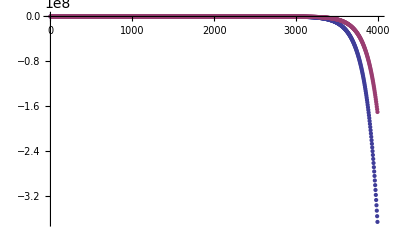

```mathematica
f[u_,r_]:=Simplify[{(Z*a/r+2-Enn)*u[[2]]-k/r*u[[1]],
k/r*u[[2]]+(Enn-Z*a/r)*u[[1]]}];
k=-1;Z=1;U=.
n=1000;
h=4000/n;
Enn=13.605/M;
u={(91.35044102604739 (-3.662751763692355+Enn) (1.6262886176197724+Enn))/((-0.0109728221664999+Enn) (181.38339842774778+Enn)),-1};
r=1;U={{r,u}};
Do[
k0=h*f[u,r];k1=h*f[u+k0/2,r+h/2];k2=h*f[u+k1/2,r+h/2];k3=h*f[u+k2,r+h];
u+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[U,{r,u}],{n}];x=.;
ListPlot[Table[{#[[1]],137^(i-2)*#[[2,i]]}&/@U[[1;;n]],{i,2}]//N,PlotRange->All]
```

```mathematica
Sum[A[n]*r^n/n!,{n,0,10}]
```

A[0]+r A[1]+1/2 r^2 A[2]+1/6 r^3 A[3]+1/24 r^4 A[4]+1/120 r^5 A[5]+1/720 r^6 A[6]+(r^7 A[7])/5040+(r^8 A[8])/40320+(r^9 A[9])/362880+(r^10 A[10])/3628800

```mathematica
D[%,{r,4}]
```

A[4]+r A[5]+1/2 r^2 A[6]+1/6 r^3 A[7]+1/24 r^4 A[8]+1/120 r^5 A[9]+1/720 r^6 A[10]

```mathematica
Sum[A[n+4]*r^n/n!,{n,0,10}]
```

A[4]+r A[5]+1/2 r^2 A[6]+1/6 r^3 A[7]+1/24 r^4 A[8]+1/120 r^5 A[9]+1/720 r^6 A[10]+(r^7 A[11])/5040+(r^8 A[12])/40320+(r^9 A[13])/362880+(r^10 A[14])/3628800